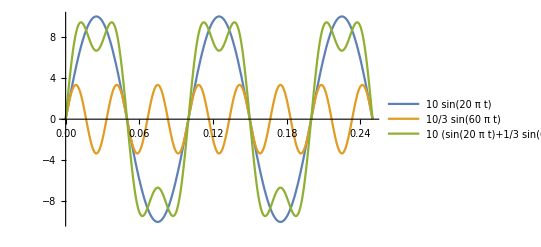

```mathematica
Module[{v},v=10;
Plot[
Evaluate[ 
10*Append[
Table[1/i Sin[2Pi (i v)t],{i,1,3,2}],
Sum[1/i Sin[2Pi (i v)t],{i,1,3,2}]]],
{t,0,0.25},PlotLegends->"Expressions"]]
```

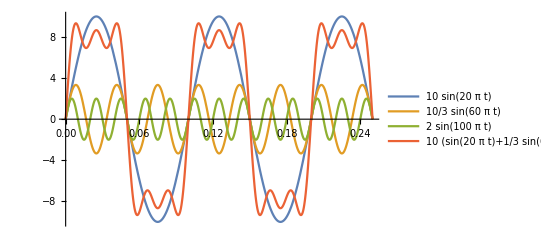

```mathematica
Module[{v},v=10;
Plot[
Evaluate[ 
10*Append[
Table[1/i Sin[2Pi (i v)t],{i,1,5,2}],
Sum[1/i Sin[2Pi (i v)t],{i,1,5,2}]]],
{t,0,0.25},PlotLegends->"Expressions"]]
```

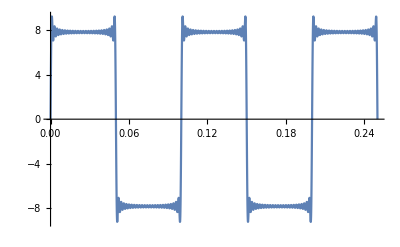

```mathematica
Module[{v,list},v=10;
list=10*Sum[1/i Sin[2Pi (i v)t],{i,1,49,2}];
Plot[list,{t,0,0.25}]]
```

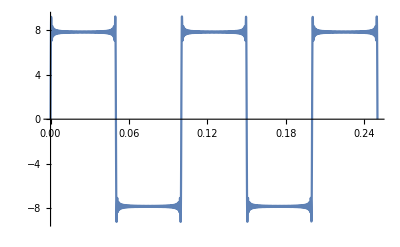

```mathematica
Module[{v,list},v=10;
list=10*Sum[1/i Sin[2Pi (i v)t],{i,1,99,2}];
Plot[list,{t,0,0.25}]]
```